## General-Purpose Functions

```mathematica
fourPointDataDir=FileNameJoin[{NotebookDirectory[]}];
```

```mathematica
fourPointDataDir="/home/gabriele/Documents/GitHub/ML-correlator/consolidated_data"
```

/home/gabriele/Documents/GitHub/ML-correlator/consolidated_data

```mathematica
SetDirectory[fourPointDataDir];

niceTime[timeInSec_]:=If[timeInSec<($TimeUnit/100)||Not[NumericQ[timeInSec]]||Precision[timeInSec]==0,"",Block[{measure=Select[Transpose[{(Quotient[Mod[timeInSec,#1],#2]&@@@Partition[{timeInSec 10,3.15569277216*^7,3600*24.,3600.,60.,1.,10^-3,10.^-6,10.^-9},2,1]),{" years"," days"," hours"," minutes"," seconds"," ms"," μs"," ns"}}],#[[1]]>0&]},If[Length[measure]>0,Row[Row[#,""]&/@measure[[1;;Min[2,Length[measure]]]],", "],""]]];
map[function_,list_]:=If[Length[list]>0,Module[{monitor=0,len=Length[list],newFcn,t00=AbsoluteTime[]},newFcn[i_]:=(monitor=i;function[list[[i]]]);Monitor[Map[newFcn,Range[len]],(Column[{ProgressIndicator[(monitor-1)/len,ImageSize->{1250,30},ImageMargins->0,BaselinePosition->Center],If[monitor≥1,Row[{If[monitor>1,Row[{niceTime[Round[AbsoluteTime[]-t00]]," so far; approx. ",niceTime[Round[((AbsoluteTime[]-t00)/(monitor-1))*(len-monitor+1)]]," remaining."}],"                                              "]," (",monitor-1,"/",len,")"}],""]},Alignment->Left,Spacings->0.1])]],Map[function,list]];
littleGroup[graph_]:=Block[{num=Numerator[graph],den=Denominator[graph]},num=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[num][[2;;-1]]);den=Join@@(Function[{y,z},y&/@Range[z]]@@@FactorList[den][[2;;-1]]);-(Count[num,#,{0,∞}]-Count[den,#,{0,∞}])&/@Sort[DeleteDuplicates[Flatten[List@@@Cases[graph,_x,{0,∞}]]]]];
```

## Basic Data Functions

```mathematica
planarGraphDials[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_dials_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[planarGraphDials[loop],ReadList[fileName]],{{}}]];
planarGraphEdges[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("fGraph_edges_"<>ToString[loop]<>".tex"))}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];Set[planarGraphEdges[loop],(raw/.rule)]),{{}}]];
fGraphNums[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}],raw,rule},If[FileExistsQ[fileName],(raw=ReadList[fileName];rule=Thread[Rule[Range[Binomial[4+loop,2]],Subsets[Range[4+loop],{2}]]];raw=Times@@@#&/@(x@@@#&/@#&/@(raw/.rule));Set[fGraphNums[loop],raw]),{{}}]];
fGraphList[loop_]:=If[FileExistsQ[FileNameJoin[{fourPointDataDir,("fGraph_nums_"<>ToString[loop]<>".tex")}]],Set[fGraphList[loop],(Join@@(fGraphNums[loop](1/(Times@@@(x@@@#&/@planarGraphEdges[loop])))))],{{}}];

amplitudeCoefficients[loop_]:=Block[{fileName=FileNameJoin[{fourPointDataDir,(("amplitudeCoefficients_"<>ToString[loop]<>".tex"))}]},If[FileExistsQ[fileName],Set[amplitudeCoefficients[loop],(<<(fileName))],{}]];
```

```mathematica
(* This takes you from the fnum list to the dialnumber list position *)
fnumtodialnum[loop_,fnum_]:=Position[Table[Range[#[[i]]+1,#[[i+1]]],{i,1,Length[#]-1}]&@Prepend[Accumulate[Length/@fGraphNums[loop]],0],fnum][[1]]
dialnumtofnum[loop_,{dial_,num_}]:=(Table[Range[#[[i]]+1,#[[i+1]]],{i,1,Length[#]-1}]&@Prepend[Accumulate[Length/@fGraphNums[loop]],0])[[dial,num]]
```

```mathematica
Length/@fGraphNums[6]
```

{3,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1}

## Graph Analysis

```mathematica
takeSmallest[x_,p_Integer]:= Take[Sort[x],p]
```

```mathematica
graphIsomorphisms[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,((bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])),(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&])])])]];
graphIsomorphism[fcnList__]/;(Length[{fcnList}]==2):=Block[{factors={fcnList},isoList,bases,nums,baseLabels=DeleteDuplicates[Cases[{fcnList}[[1]],x[y__]:>y,{0,∞}]]},If[Length[DeleteDuplicates[factors]]==1,Thread[Rule[baseLabels,baseLabels]],(Which[Not[SameQ@@(LeafCount/@factors)],{},True,(bases=(Function[{q},List@@@DeleteDuplicates[Cases[Denominator[q],x[y__],{0,∞}]]]/@factors);nums=(factors*((Times@@(x@@@#))&/@bases));bases=Graph[UndirectedEdge@@@#]&/@bases;isoList=(FindGraphIsomorphism[#1,#2,All]&@@bases);If[Length[isoList]==0,{},(isoList=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@isoList);isoList=Select[isoList,SameQ[nums[[2]],(nums[[1]]/.{x[y__]:>(x@@Sort[{y}/.#])})]&,1])])])]];
graphEquivalentQ[fcnList__]/;(Length[{fcnList}]==2):=Not[graphIsomorphism[fcnList]==={}];
distinctGraphs[seedList_]:=DeleteDuplicates[seedList,graphEquivalentQ];
graphAutomorphisms[graph_]:=graphIsomorphisms[graph,graph];
graphSymmetryFactor[graph_]:=Length[graphAutomorphisms[graph]];
canonicalizeGraph[graph_]:=Block[{baseEdges=List@@@DeleteDuplicates[Cases[Denominator[graph],x[y__],{0,∞}]],baseLabels,baseGraph,auto},baseLabels=DeleteDuplicates[Flatten[baseEdges]];baseGraph=Graph[UndirectedEdge@@@baseEdges];auto=(Function[{iso},Thread[Rule@@(baseLabels/.{{},iso})]]/@FindGraphIsomorphism[baseGraph,CanonicalGraph[baseGraph]])[[1]];graph/.{x[q__]:>x@@(Sort[{q}/.auto])}];

orderedVertsToFaces[dialList_]:=Block[{edgeRules,fullEdgeList},edgeRules=Join@@Table[(Rule[{#1,j},{j,#2}]&@@@Partition[dialList[[j]],2,1,1]),{j,Length[dialList]}];fullEdgeList=edgeRules[[All,1]];Sort@DeleteDuplicates[Function[{start},(Function[{term},Sort[Partition[Reverse@term,Length[term],1,1]][[1]]]@DeleteDuplicates[Join@@NestWhile[Append[#,(#[[-1]]/.edgeRules)]&,{start},Length[DeleteDuplicates[#]]==Length[#]&]])]/@fullEdgeList]];
```

```mathematica
fgraphtograph[fgraph_]:=Graph[(List@@Denominator[fgraph])/.x->List]
```

NB Problem with canonicalise graph . See two examples below . Is it not doing numerators?

New canonicalise: canonicalisefgraph . First canonicalises the denominator using inbuilt mathematica . Then applies the autumorphism group of the resulting graph to the numerator and selects the first in the ordered list . This seems to work...

```mathematica
numeratormonomialtolist[numerator_]:=ConstantArray@@@Transpose[{Cases[#,x[_,_],Infinity],Exponent[#,Cases[#,x[_,_],Infinity]]}]&@(numerator)//Flatten
```

```mathematica
canonicalizefgraph[fgraph_]:=Module[{dengraphcan,dengraphtocanisomorphism,dencan,numcan1,numcan,dengraph,numedgelist},
dengraph=fgraphtograph[fgraph];
dengraphcan=CanonicalGraph[dengraph];
dengraphtocanisomorphism=((FindGraphIsomorphism[dengraph,dengraphcan]//Normal)[[1]]);
numedgelist=numeratormonomialtolist[Numerator[fgraph]];
numcan1=numedgelist/.dengraphtocanisomorphism/.x[a_,b_]:>x[b,a]/;(b<a);
dencan=Times@@(EdgeList[dengraphcan]/.UndirectedEdge->x);
numcan=takeSmallest[Times@@@PermutationReplace[numcan1,GraphAutomorphismGroup[dengraphcan]]/.x[exp__]:>x[Sequence@@Sort[{exp}]]/;(Sort[{exp}]=!={exp}),1][[1]];
Times@@numcan/dencan]
```

```mathematica
g1=(x[4,9] x[5,6] x[7,8] x[10,11]^2)/(x[1,6] x[1,7] x[1,8] x[1,9] x[2,3] x[2,4] x[2,10] x[2,11] x[3,5] x[3,10] x[3,11] x[4,6] x[4,8] x[4,10] x[4,11] x[5,7] x[5,9] x[5,10] x[5,11] x[6,7] x[6,8] x[6,10] x[7,9] x[7,10] x[8,9] x[8,11] x[9,11]);g2=(x[4,5] x[6,9] x[7,8] x[10,11]^2)/(x[1,4] x[1,5] x[1,6] x[1,7] x[2,3] x[2,9] x[2,10] x[2,11] x[3,8] x[3,10] x[3,11] x[4,6] x[4,7] x[4,9] x[4,11] x[5,6] x[5,7] x[5,8] x[5,10] x[6,8] x[6,11] x[7,9] x[7,10] x[8,10] x[8,11] x[9,10] x[9,11]);
graphEquivalentQ[g1,g2]
canonicalizeGraph/@{g1,g2};
Equal@@%//Simplify
canonicalizefgraph/@{g1,g2};
Equal@@%//Simplify
```

True

((x[4,7] x[5,8] x[6,9]-x[4,9] x[5,6] x[7,8]) x[10,11])/(x[1,6] x[1,7] x[1,8] x[1,9] x[2,3] x[2,4] x[2,10] x[2,11] x[3,5] x[3,10] x[3,11] x[4,6] x[4,8] x[4,10] x[4,11] x[5,7] x[5,9] x[5,10] x[5,11] x[6,7] x[6,8] x[6,10] x[7,9] x[7,10] x[8,9] x[8,11] x[9,11])==0

True

```mathematica
Clear[fGraphListcan]
fGraphListcan[loop_]:=fGraphListcan[loop]=canonicalizefgraph/@fGraphList[loop]
```

```mathematica
(* cycles dial (or face) so that vertex vertex ve is first *)

cycle[dial_,ve_]:=If[MemberQ[dial,ve],Join[Take[dial,{Position[dial,ve][[1,1]],Length[dial]}],Take[dial,{1,Position[dial,ve][[1,1]]-1}]],dial]
```

## All graphs relaed via cusp rule

```mathematica
allrelatedfgs[{4,1}]
```

```mathematica
myComplement[full_,todel_]:=Fold[Delete[#1,Position[#1,#2,1,1]]&,full,todel]
```

```mathematica
(* vertices of double triangle {v_,w_,v1_,v2_} with v1,v2 left and right (2 valent) v,w top and bottom (3 valent) so v,w merge to 1 vertex in the cusp limit 
Output = {coeffs of all related l loop graphs, coeff of shrunk graph, graph numbers of all related graphs, graph number of shrunk graph. They need to be correctly oriented for it to work...}
 IN: allrelatedfgs[{4,1},{6,7,1,3}]
  OUT: {{1,-1},0,{4,{1,2}},{3,0}}
*)

allrelatedfgs[{loop_,fgn_},{v_,w_,v1_,v2_}]:=Module[{n,fgraph,dials,faces,facesv,facesw,upperfaces,lowerfaces,upperbigface,lowerbigface,newnumeratorpointsupper,newnumeratorpointslower,newedges,newfgraphden,existingnum,existingnumlist,existingnumeratorpointstov,existingnumeratorpointstow,remainignnumerators,allnumeratorpointstovandw,numeratorlist,fgraphs,fgraphscan,fgnums,fgnums1,shrunkgraphs,fgshrunkgnum,coeff,coeffs},n=loop+4;
fgraph=fGraphList[loop][[fgn]];
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
faces=orderedVertsToFaces[dials];
facesv=cycle[#,v]&/@Select[faces,MemberQ[#,v]&];
facesw=cycle[#,w]&/@Select[faces,MemberQ[#,w]&];
upperfaces=Drop[Table[Select[facesv,#[[2]]==vn&][[1]],{vn,cycle[dials[[v]],v1]}],-2];
upperbigface=Join[{v,v1},Flatten[Drop[#,2]&/@upperfaces]];
lowerfaces=Drop[Table[Select[facesw,#[[2]]==wn&][[1]],{wn,cycle[dials[[w]],v2]}],-2];
lowerbigface=Join[{w,v2},Flatten[Drop[#,2]&/@lowerfaces]];
newnumeratorpointsupper=Select[upperbigface,Not[MemberQ[Join[dials[[v]],dials[[w]]],#]]&];
newnumeratorpointslower=Select[lowerbigface,Not[MemberQ[Join[dials[[v]],dials[[w]]],#]]&];
newedges=Join[(x[v,#]&/@newnumeratorpointsupper),(x[w,#]&/@newnumeratorpointslower)];
newfgraphden=Denominator[fgraph]*(Times@@newedges);
existingnum=fGraphNums[loop][[Sequence@@fnumtodialnum[loop,fgn]]];
existingnumlist=({existingnum}/.Times->List)/.a_^b_:>ConstantArray[a,b]//Flatten;
existingnumeratorpointstov=Join[Cases[existingnumlist,x[v,a_]:>a,Infinity],Cases[existingnumlist,x[a_,v]:>a,Infinity]];
existingnumeratorpointstow=Join[Cases[existingnumlist,x[w,a_]:>a,Infinity],Cases[existingnumlist,x[a_,w]:>a,Infinity]];
remainignnumerators=Times@@Select[existingnumlist,Not[MemberQ[#,v]]&&Not[MemberQ[#,w]]&];
allnumeratorpointstovandw=Join[newnumeratorpointsupper,newnumeratorpointslower,existingnumeratorpointstov,existingnumeratorpointstow];
numeratorlist=DeleteDuplicates[(Product[x[v,i],{i,#}]Product[x[w,i],{i,myComplement[allnumeratorpointstovandw,#]}])&/@Subsets[allnumeratorpointstovandw,{Length[newnumeratorpointsupper]+Length[existingnumeratorpointstov]}]/.x[a_,b_]:>x[b,a]/;(b<a)];
fgraphs=(numeratorlist remainignnumerators)/newfgraphden/.x[a_,b_]:>x[b,a]/;(b<a);
fgraphscan=canonicalizefgraph/@fgraphs;
fgnums1=If[#==={},(Print["fgraph not identified: ","loop=",loop," fg number=",fgn," double triangle vertices= ",v,w,v1,v2]);#,#]&/@(Position[fGraphListcan[loop],#]&/@fgraphscan);
fgnums=Flatten[fgnums1];
shrunkgraphs=(fgraphs /.x[a_,b_]:>x[a/.{w->v},b/.{w->v}])(x[v,v]x[v1,v]x[v2,v])/x[v1,v2]/.x[a_,b_]:>x[a/.{n->w},b/.{n->w}]/.x[a_,b_]:>x[b,a]/;a>b;
If[Length[Union[shrunkgraphs]]=!=1,Print["There are different shrunk graphs...",{coeffs,coeff,{loop,fgnums},{loop-1,fgshrunkgnum}}]];
fgshrunkgnum=If[#==={},0,#[[1,1]]]&@Position[fGraphListcan[loop-1],canonicalizefgraph[shrunkgraphs[[1]]]];
coeff=If[fgshrunkgnum===0,0,amplitudeCoefficients[loop-1][[fgshrunkgnum]]];
coeffs=amplitudeCoefficients[loop][[fgnums]];
If[Total[coeffs]=!=coeff,Print["Not matching the cusp equation",{coeffs,coeff,{loop,fgnums},{loop-1,fgshrunkgnum}}]];
{coeffs,coeff,{loop,fgnums},{loop-1,fgshrunkgnum}}]
```

```mathematica
detectdoubletriangles[{loop_,fgn_}]:=Module[{fgraph,dials,triangles},fgraph=fGraphList[loop][[fgn]];
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
triangles=Select[orderedVertsToFaces[dials],Length[#]==3&];
Select[Subsets[triangles,{2}],Length[Intersection[#[[1]],#[[2]]]]==2&]]
```

```mathematica
detectnonisomorphicdoubletriangles[{loop_,fgn_}]:=Module[{fgraph,dials,triangles,alldts,dtscurrent,dtsnoniso,autos},
fgraph=fGraphList[loop][[fgn]];
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
triangles=Select[orderedVertsToFaces[dials],Length[#]==3&];
alldts=Select[Subsets[triangles,{2}],Length[Intersection[#[[1]],#[[2]]]]==2&];
autos=graphAutomorphisms[fGraphList[loop][[fgn]]];
dtscurrent=alldts;
dtsnoniso={};
While[Length[dtscurrent]>0,dtsnoniso=Append[dtsnoniso,dtscurrent[[1]]];dtscurrent=Complement[dtscurrent,Table[dtscurrent[[1]]/.ii,{ii,autos}],SameTest->((Sort/@{#1[[1]],#1[[2]]} ==Sort/@{#2[[1]],#2[[2]]})||(Sort/@{#1[[2]],#1[[1]]} ==Sort/@{#2[[1]],#2[[2]]}) &) ]];
dtsnoniso]
```

```mathematica
doubletriangletovwv1v2[dt_]:=Module[{tallied=Tally[Flatten[#]]&@dt,vw,dtcycledtov},vw=Select[#,#[[2]]==2&][[All,1]]&@(tallied);dtcycledtov={cycle[dt[[1]],vw[[1]]],cycle[dt[[2]],vw[[1]]]};If[dtcycledtov[[1,2]]!=vw[[2]],{vw[[1]],vw[[2]],dtcycledtov[[2,3]],dtcycledtov[[1,2]]},{vw[[1]],vw[[2]],dtcycledtov[[1,3]],dtcycledtov[[2,2]]}]]
```

```mathematica
allsidewaysrelationstofgraph[{loop_,fgn_}]:=
Module[{dts=detectnonisomorphicdoubletriangles[{loop,fgn}]},allrelatedfgs[{loop,fgn},doubletriangletovwv1v2[#]]&/@dts]
```

```mathematica
highlightgraph[{loop_,fgn_},dt_]:=Column[{HighlightGraph[PlanarGraph[fgraphtograph[fGraphList[loop][[fgn]]],VertexLabels->"Name"],UndirectedEdge@@@Join[Subsets[dt[[1]],{2}],Subsets[dt[[2]],{2}]]],Numerator[fGraphList[loop][[fgn]]]}]
```

```mathematica
highlightalldoubletriangles[{loop_,fgn_}]:=highlightgraph[{loop,fgn},#]&/@detectnonisomorphicdoubletriangles[{loop,fgn}]
```

{{{1},1,{4,{1}},{3,1}},{{1},1,{4,{1}},{3,1}},{{1},1,{4,{1}},{3,1}},{{1,-1},0,{4,{1,2}},{3,0}}}

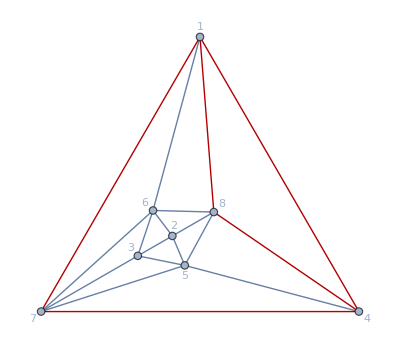
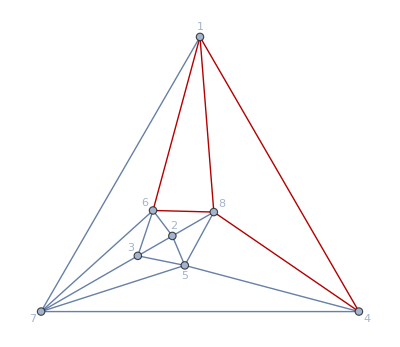
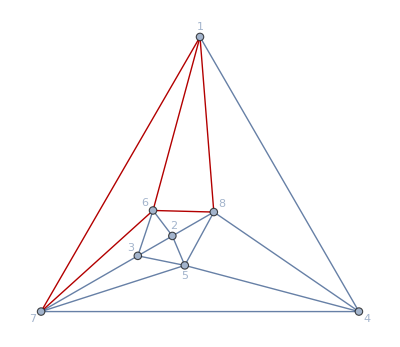
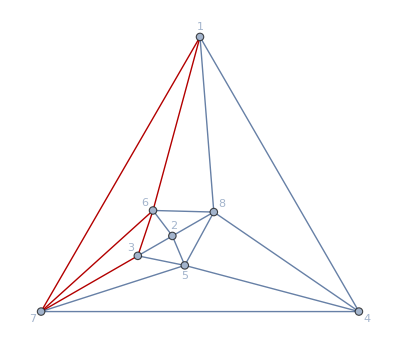
{-Graphics-
x[5,6] x[7,8],-Graphics-
x[5,6] x[7,8],-Graphics-
x[5,6] x[7,8],-Graphics-
x[5,6] x[7,8]}

```mathematica
allsidewaysrelationstofgraph[{4,1}]
highlightalldoubletriangles[{4,1}]
```

```mathematica
highlightalldoubletriangles[{6,#}]&/@%
```

```mathematica
Position[{1,2,{3,1,{1,4,5},3,1},1},1]
Extract[{1,2,{3,1,{1,4,5},3,1},1},%]
```

{{1},{3,2},{3,3,1},{3,5},{4}}

{1,1,1,1,1}

{{{0,-1,1},0,{6,{33,32,34}},{5,0}},{{0,0},0,{6,{33,14}},{5,0}}}

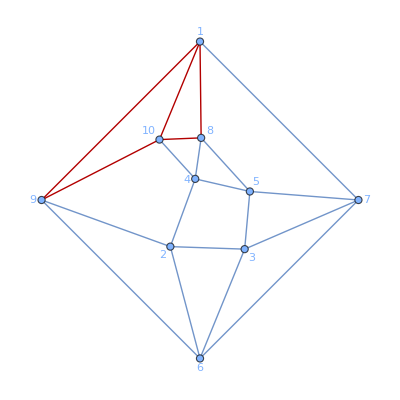
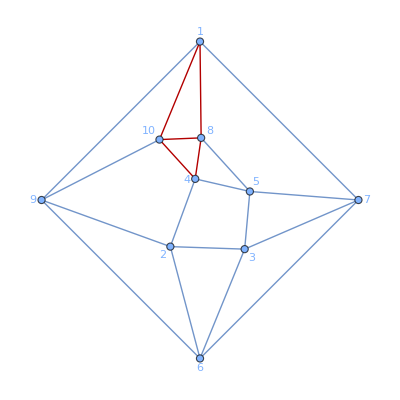
{-Graphics-
1,-Graphics-
1}

```mathematica
allsidewaysrelationstofgraph[{6,33}]
highlightalldoubletriangles[{6,33}]
```

{1,10,14,20,22,23,26,33,35,36}

{{{{0},0,{6,{1}},{5,0}},{{0,0},0,{6,{1,10}},{5,0}},{{0,0},0,{6,{1,14}},{5,0}},{{0,1},1,{6,{1,2}},{5,3}}},{{{0},0,{6,{10}},{5,0}},{{0},0,{6,{10}},{5,0}},{{0},0,{6,{10}},{5,0}},{{0},0,{6,{10}},{5,0}},{{0,0},0,{6,{10,35}},{5,0}},{{0,0},0,{6,{1,10}},{5,0}},{{0,0},0,{6,{10,20}},{5,0}},{{1,0,-1},0,{6,{9,10,32}},{5,0}},{{0,1},1,{6,{10,18}},{5,7}},{{0,-1},-1,{6,{10,32}},{5,5}}},{{{0},0,{6,{14}},{5,0}},{{0,-1},-1,{6,{14,32}},{5,5}},{{0,1,-1},0,{6,{14,11,13}},{5,0}},{{-1,0,1},0,{6,{5,14,4}},{5,0}},{{-1,0,1},0,{6,{13,14,18}},{5,0}},{{0,0},0,{6,{14,1}},{5,0}},{{0,-1},-1,{6,{14,5}},{5,5}},{{0,0},0,{6,{14,33}},{5,0}}},{{{0},0,{6,{20}},{5,0}},{{0},0,{6,{20}},{5,0}},{{0,0},0,{6,{20,10}},{5,0}},{{-1,0,1},0,{6,{21,20,19}},{5,0}}},{{{0},0,{6,{22}},{5,0}}},{{{0},0,{6,{23}},{5,0}},{{0},0,{6,{23}},{5,0}},{{0},0,{6,{23}},{5,0}},{{0,0},0,{6,{23,26}},{5,0}},{{0,1},1,{6,{23,24}},{5,3}}},{{{0},0,{6,{26}},{5,0}},{{0,0},0,{6,{26,23}},{5,0}},{{0},0,{6,{26}},{5,0}},{{-1,0,2,1,-1,-1},0,{6,{25,26,16,9,15,25}},{5,0}}},{{{0,-1,1},0,{6,{33,32,34}},{5,0}},{{0,0},0,{6,{33,14}},{5,0}}},{{{0},0,{6,{35}},{5,0}},{{0},0,{6,{35}},{5,0}},{{0},0,{6,{35}},{5,0}},{{0},0,{6,{35}},{5,0}},{{0,0},0,{6,{35,10}},{5,0}}},{{{0},0,{6,{36}},{5,0}},{{0},0,{6,{36}},{5,0}},{{0},0,{6,{36}},{5,0}}}}

{{{1}},{{1},{2},{3},{4}},{{1}},{{1},{2}},{{1}},{{1},{2},{3}},{{1},{3}},{},{{1},{2},{3},{4}},{{1},{2},{3}}}

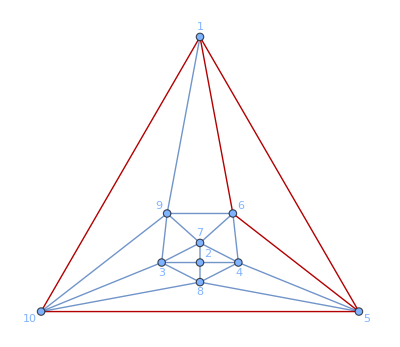
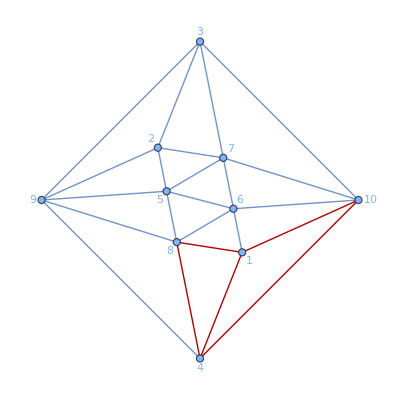
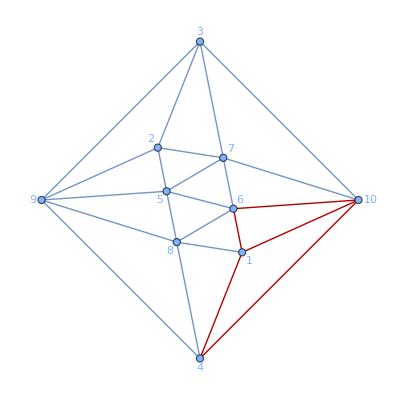
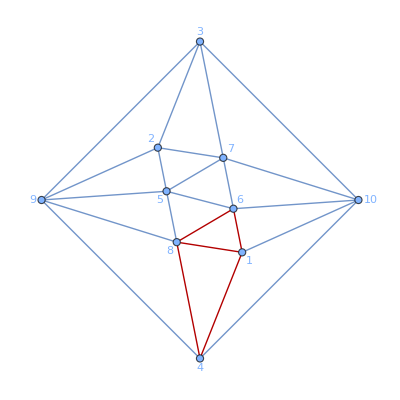
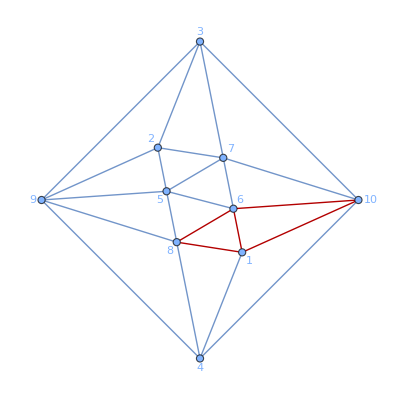
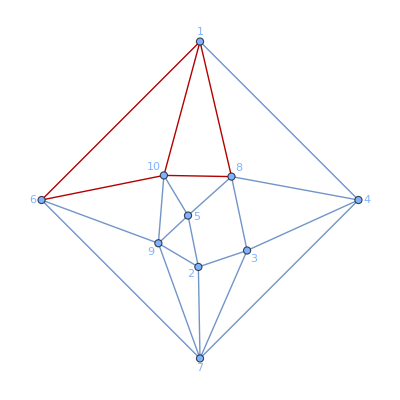
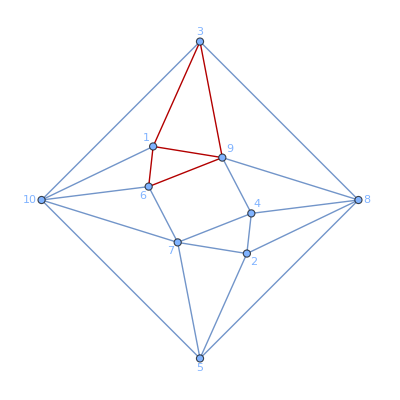
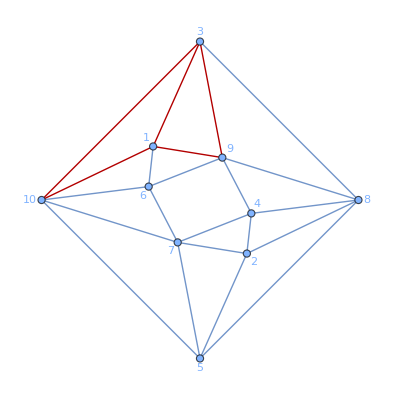
{{-Graphics-
x[3,6] x[4,10] x[5,7] x[8,9]},{-Graphics-
x[5,10] x[6,9] x[7,8],-Graphics-
x[5,10] x[6,9] x[7,8],-Graphics-
x[5,10] x[6,9] x[7,8],-Graphics-
x[5,10] x[6,9] x[7,8]},{-Graphics-
x[7,10] x[8,9]},{-Graphics-
x[7,9] x[8,10],-Graphics-
x[7,9] x[8,10]},{-Graphics-
1},{-Graphics-
x[5,7] x[6,8] x[9,10]^2,-Graphics-
x[5,7] x[6,8] x[9,10]^2,-Graphics-
x[5,7] x[6,8] x[9,10]^2},{-Graphics-
x[7,10] x[8,9],-Graphics-
x[7,10] x[8,9]},{},{-Graphics-
x[9,10],-Graphics-
x[9,10],-Graphics-
x[9,10],-Graphics-
x[9,10]},{-Graphics-
x[9,10]^2,-Graphics-
x[9,10]^2,-Graphics-
x[9,10]^2}}

```mathematica
Position[amplitudeCoefficients[6],0]//Flatten
allsidewaysrelationstofgraph[{6,#}]&/@%
Position[#,{{0},0,{6,{_}},{5,0}}]&/@%
Table[Extract[highlightalldoubletriangles[{6,%%%[[ii]]}],%[[ii]]],{ii,1,Length[%%%]}]
```

{{{0},0,{6,{1}},{5,0}},{{0,0},0,{6,{1,10}},{5,0}},{{0,0},0,{6,{1,14}},{5,0}},{{0,1},1,{6,{1,2}},{5,3}}}

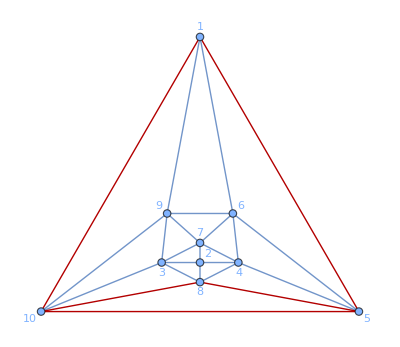
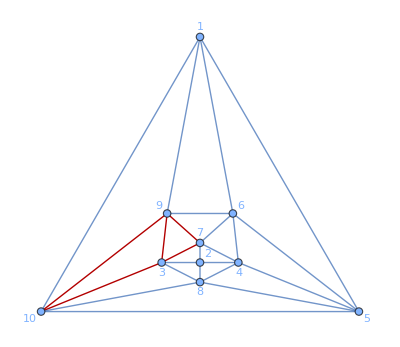
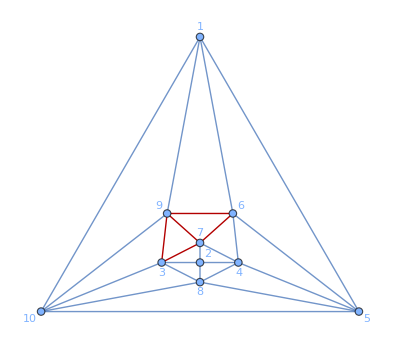
{-Graphics-
x[3,6] x[4,10] x[5,7] x[8,9],-Graphics-
x[3,6] x[4,10] x[5,7] x[8,9],-Graphics-
x[3,6] x[4,10] x[5,7] x[8,9],-Graphics-
x[3,6] x[4,10] x[5,7] x[8,9]}

```mathematica
allsidewaysrelationstofgraph[{6,1}]
highlightalldoubletriangles[{6,1}]
```

Don’t need the below, but leave here in case we want later:

```mathematica
detectcusps[{loop_,fgn_}]:=Module[{fgraph,dials,cusps},fgraph=fGraphList[loop][[fgn]];
dials=planarGraphDials[loop][[fnumtodialnum[loop,fgn][[1]]]];
cusps=Table[{ii,#[[1]],#[[2]]}&/@Subsets[dials[[ii]],{2}],{ii,loop+4}]]
```

```mathematica
detectcusps[{4,1}]
```

{{{1,4,8},{1,4,6},{1,4,7},{1,8,6},{1,8,7},{1,6,7}},{{2,3,6},{2,3,8},{2,3,5},{2,6,8},{2,6,5},{2,8,5}},{{3,2,5},{3,2,7},{3,2,6},{3,5,7},{3,5,6},{3,7,6}},{{4,1,7},{4,1,5},{4,1,8},{4,7,5},{4,7,8},{4,5,8}},{{5,2,8},{5,2,4},{5,2,7},{5,2,3},{5,8,4},{5,8,7},{5,8,3},{5,4,7},{5,4,3},{5,7,3}},{{6,1,8},{6,1,2},{6,1,3},{6,1,7},{6,8,2},{6,8,3},{6,8,7},{6,2,3},{6,2,7},{6,3,7}},{{7,1,6},{7,1,3},{7,1,5},{7,1,4},{7,6,3},{7,6,5},{7,6,4},{7,3,5},{7,3,4},{7,5,4}},{{8,1,4},{8,1,5},{8,1,2},{8,1,6},{8,4,5},{8,4,2},{8,4,6},{8,5,2},{8,5,6},{8,2,6}}}